# Reverse Dictionary

## Data

Data was taken from the site of the following paper: Hill, F. Cho, KH., Korhonen, A., and Bengio, Y. Learning to Understand Phrases by Embedding the Dictionary. 2016. Transactions of the Association for Computational Linguistics (TACL). Originally it was recollected via WordNik API in Python.

## Proof of Concept

For this first proof of concept analysis, we used 50 of the most common nouns in the English language. We chose the 50 with more definitions assigned to them so that the training can be more efficient. The number of definitions per word was normalized to the minimum among the maximum number of definitions for each word. This was so there would be no bias in the data.

Global Set

```mathematica
simplePath=FileNameJoin[{NotebookDirectory[],"training_data","60Def50Words.csv"}];
rawData=Import[simplePath];
```

```mathematica
associate[elem_]:=Last[elem]-> First[elem];
```

```mathematica
wordDefSet=Map[associate, rawData];
RandomSample[wordDefSet, 10]//TableForm
```

the act of serving the occupation of a servant the performance of labor for the benefit of another or at another s command attendance of an inferior hired helper slave etc on a superior employer master or the like also spiritual obedience and love→service
 appearance of grandeur or dignity pomp→state
 a section of code representing one of the actions of a conditional switch→case
 a fitting consisting of a loop of metal or other material suitable for receiving a hook or the passage of a cord or line→eye
 relating to or being mother→mother
 to substitute another thing or things for shift cause to be replaced by another as to change the clothes or one suit of clothes for another to change one s position→change
 to divide in two→part
 to look at someone or something as if with the intent to do something with that person or thing→eye
 an ideal point of a graph or other complex→end
 a meaningful stare or look→eye

```mathematica
wordset=DeleteDuplicates[Map[Last,wordDefSet]];
```

Testing Set

```mathematica
simpleTestingSet=Select[Normal[DeleteDuplicates[Association[RandomSample[wordDefSet]]]],Not[StringContainsQ[Last[#],"ï»¿"]]&];
RandomSample[simpleTestingSet, 10]//TableForm
```

in a narrow use the children of the same parents considered collectively apart from the parents as they a husband and wife have a large family to care for a family of children→family
 rational and balanced sensible came to a level appraisal of the situation keeps a level head in an emergency→level
 to transact official business dishonestly for private profit→job
 to seek to learn by memorizing the facts principles or words of apply the mind to learning store in the memory either generally or verbatim as to study a book a language history etc to study a part in a play or a piece for recitation→study
 a hysterical malady→mother
 a song especially a solo an aria→air
 a female servant a maid→girl
 hand down to make and pronounce an official decision especially a court verdict→hand
 examination by torture or the application of torture to prisoners under criminal accusation in order to extort confession→question
 to move or effect against resistance or inertia forced my foot into the shoe→force

Training Set

```mathematica
simpleTrainingSet=Select[wordDefSet,Not[MemberQ[simpleTestingSet,First[#]->_]]&&Not[StringContainsQ[Last[#],"ï»¿"]]&];
RandomSample[simpleTrainingSet, 10]//TableForm
```

hence any certain person who is regarded as being opposed or antagonistic to another→party
 change hands to pass from one owner to another→change
 the fluid which we breathe and which surrounds the earth the atmosphere→air
 commercial industrial or professional dealings new systems now being used in business→business
 to exereise the faculty of reason make rational deductions think or choose rationally use intelligent discrimination→reason
 to cast lots→lot
 a brood→eye
 a mark or dot used in printing or writing for punctuation especially a period→point
 a total a sum the number of feet in a mile→number
 the difference in depth of a liquid at two given points→head

Simplest Approach

Simplest Approach consists of using built in function Classify to attempt to solve the problem.

```mathematica
classifier=Classify[simpleTrainingSet,PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

```mathematica
cm=ClassifierMeasurements[classifier,simpleTestingSet]
```

ClassifierMeasurementsObject[…]

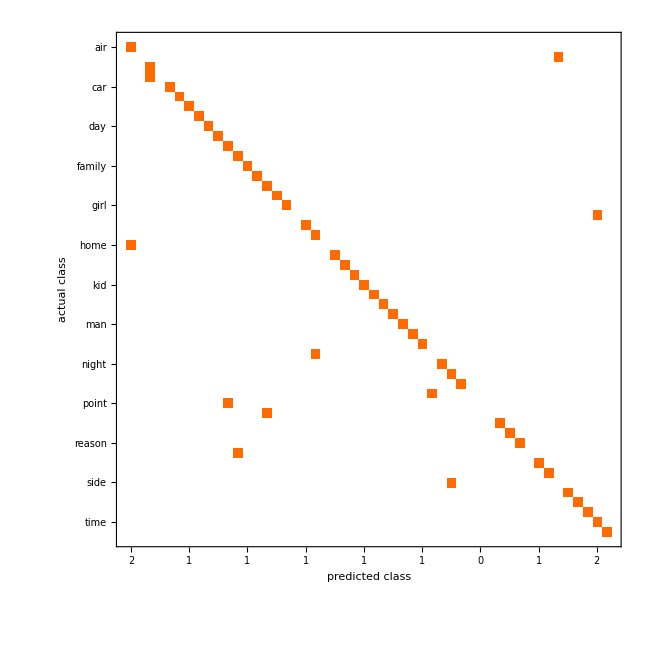

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
ClassifierInformation[classifier]
```

Classifier information
Method | Markov
Number of classes | 50
Number of features | 1
Number of training examples | 2944
Number of tokens | 5694
Markov order | 1
Regularization method | Katz

Apparently this does it, and the performance seems pretty good. Now, this model might be over-fitted, so we must test with data it has never seen.

```mathematica
ClassifierMeasurements[classifier,simpleTestingSet,"Accuracy"]
```

0.8

```mathematica
ClassifierMeasurements[classifier,simpleTestingSet,"F1Score"]
```

<|air→0.666667,back→0.,book→0.666667,business→0.,car→1.,case→1.,change→1.,company→1.,day→1.,end→1.,eye→0.666667,face→0.666667,family→1.,father→1.,force→0.666667,game→1.,girl→1.,group→0.,hand→1.,head→0.666667,home→0.,house→1.,issue→1.,job→1.,kid→1.,law→1.,level→1.,lot→1.,man→1.,minute→1.,mother→1.,name→0.,night→1.,number→0.666667,part→1.,party→0.,point→0.,power→0.,president→1.,question→1.,reason→1.,right→0.,school→1.,service→1.,side→0.,state→1.,study→1.,thing→1.,time→0.666667,word→1.|>

Test with own definitions

```mathematica
textSimple="";
InputField[Dynamic[textSimple],String,ContinuousAction->True]
```

```mathematica
Dynamic[Column[classifier[textSimple,"TopProbabilities"->3],Frame->All,ItemSize->{15, Automatic},Alignment->Left]]
```

Export classifier

```mathematica
Export["SimpleClassifier.m",classifier,"Package"]
```

SimpleClassifier.m

## Complete Data Set

Now that we have a working version, we can attempt to scale things up by training our model with all the data available.

Training Set

```mathematica
completePath=FileNameJoin[{NotebookDirectory[],"training_data","training_data.csv"}];
rawData=Import[completePath];
```

Lets filter just for nouns.

```mathematica
nouns=WordList["Noun"];
```

```mathematica
filtered=Select[rawData,MemberQ[nouns,First[#]]&];
RandomSample[filtered,10]
```

{{discontent, to deprive of content to make uneasy to dissatisfy},{stare, to stand out stiffly as hair be prominent be stiff stand on end bristle},{butt, the hut or shelter of the person who attends to the targets in rifle practice},{bark, bark of different plants and trees can look very different it can be rough or smooth and can have different colors},{shave, to make a passage at a close distance},{pretension, the act of pretending or laying claim the act of asserting right or title},{romanticism, see romantic school under romantic},{faint, see synonyms at blackout},{simple, plural foolish or silly behavior foolishness as to have a fit of the simples},{genesis, see table at bible}}

Lets look at the frequency of each word, as well as the average.

```mathematica
freq=Reverse[SortBy[Tally[First[#]&/@filtered],Last]];
freq[[;;10]]
```

{{go,603},{stick,412},{fall,412},{base,398},{clear,382},{do,360},{rest,344},{hang,344},{crown,342},{jacks,336}}

```mathematica
avgFreq=N[Total[Last[#]&/@freq]/Length[freq]]
```

20.431

```mathematica
trainingSet=Map[associate, filtered];
RandomSample[trainingSet,10]//TableForm
```

a swift runner a scudder→scud
 archaic gray hair→grizzle
 goods or money obtained illegally→pillage
 it has no basis in the phenomena of sound or the necessities of music as an art→key
 a holden commodore→commie
 astronomy the passage of a celestial body across the observer s meridian→transit
 specifically a furnace stove or other device for heating drying or warning buildings rooms drying houses fruit evaporators or parts of machines as the calendering rolls of a paper mill→heater
 in organ building a flute pipe as distinguished from a mouth pipe or reed pipe→flue
 a cosmetic or medicinal preparation for dressing the hair→hairdressing
 a pleasing taste flavor that gratifies the palate hence enjoyable quality power of pleasing→relishing

```mathematica
Length[trainingSet]
```

425333

```mathematica
wordset=DeleteDuplicates[Map[Last,trainingSet]];
Length[wordset]
```

20818

Testing Set

```mathematica
rawTesting=Import["Personal\\WSS\\wss_project\\test_data\\testing_data.csv"];
```

```mathematica
filteredTest=Select[rawTesting,MemberQ[nouns,First[#]]&];
```

```mathematica
testingSet=Map[associate, filteredTest];
RandomSample[testingSet, 10]//TableForm
```

a material that is normally white made from trees and useful for writing on→paper
 a group of men who fight together in the name of a country→army
 the time at the end of the day when the sun goes down and people sleep→night
 to regularly provide people or an organization with things→supply
 an animal that is commonly kept as a pet and is famous for loyalty to humans→dog
 one of the directions on a compass that points right when you look at it→east
 a type of deadly illness that spreads through the body by abnormal multiplication of cells→cancer
 a strong emotional feeling of physical or mental attraction towards somebody→love
 popular drink made by putting leaves in hot water→tea
 all of the information or facts that somebody might have in their head→knowledge

Classify

As it proved to be working for the small dataset, we can try again with Classify.

```mathematica
cl=Classify[trainingSet,PerformanceGoal->"Quality"]
```

Classify::bdfmt: Argument filtered should be a rule, a list of rules, or an association.

Classify[filtered,PerformanceGoal→Quality]

```mathematica
ClassifierInformation[cl,"TrainingTime"]
```

3954.02 s

```mathematica
ClassifierMeasurements[cl,testingSet,"Accuracy"]
```

0.

Test with own definitions

```mathematica
text="";
InputField[Dynamic[text],String,ContinuousAction->True]
```

```mathematica
Dynamic[Column@cl[text,"TopProbabilities"->10]]
```

## Playing with variance and performance

Lets look at the whole data set.

```mathematica
completeDataFreq=Reverse[SortBy[Tally[First[#]&/@rawData],Last]];
completeDataFreq[[;;10]]
```

{{var,648},{go,603},{nox,474},{points,438},{rounds,424},{stick,412},{fall,412},{bak,408},{det,404},{base,398}}

```mathematica
Length[completeDataFreq]
```

67713

```mathematica
completeDataMean=N[Mean[Last[#]&/@completeDataFreq]]
```

12.5895

```mathematica
completeDataVar=N[Variance[Last[#]&/@completeDataFreq]]
```

430.875

Filtering for nouns.

```mathematica
Length[freq]
```

20818

```mathematica
filteredMean=N[Mean[Last[#]&/@freq]]
```

20.431

```mathematica
filteredVar=N[Variance[Last[#]&/@freq]]
```

759.839

Variance grew, so this means that the performance of our classifier might worsen.

We can try to balance things by taking only words that satisfy having more than a certain number of definitions.

```mathematica
getBalancedList[noElem_]:=Module[{wordSet,wordCounter,resultList,elem,word},(
	wordSet=First[#]&/@Select[freq,Last[#]≥noElem&];
	wordCounter=<||>;
	resultList={};
	For[i=1,i≤Length[filtered],i++,
		elem=filtered[[i]];
		word=First[elem];
		If[MemberQ[wordSet,word],
			If[KeyExistsQ[wordCounter,word],
				If[wordCounter[[word]]≤noElem,
					AppendTo[resultList,elem];
					wordCounter[[word]]+=1],
			AppendTo[wordCounter,word->1]
			]
		]
	];
	resultList
)]
```

```mathematica
balanced=getBalancedList[50];
RandomSample[balanced,10]
```

{{beaver, it is semi aquatic meaning some of the time it lives in water some of the time it lives on land},{piping, having a shrill whistling sound},{cold, chilled by refrigeration or ice cold beer},{scouring, to search through or over thoroughly the detective scoured the scene of the crime for clues},{carry, to hold and move the body or a part of it in a particular way carried her head proudly},{hollow, to shout to hollo},{tackle, equipment or gear in general a combination of appliances used of arms and armor harness anglers outfit see fishing tackle many mechanical devices etc},{rocket, a rocket propelled firework a skyrocket},{plant, slang to deliver a blow or punch},{tiger, a kind of growl or screech after cheering}}

```mathematica
Length[balanced]
```

86686

```mathematica
wordset=DeleteDuplicates[Map[First,balanced]];
balancedWordDef=Map[associate, balanced];
```

Testing set

```mathematica
balTestingSet=Select[Normal[DeleteDuplicates[Association[RandomSample[balancedWordDef]]]],Not[StringContainsQ[Last[#],"ï»¿"]]&];
RandomSample[testingSet, 10]//TableForm
```

a large body of water that is surrounded by land→lake
 the sister of your mother→aunt
 the organ in the body that is stores and digests food→stomach
 the limbs that birds move in order to fly→wing
 the bottom part of the leg on which people walk→foot
 a large building made of stones that is easy for an army to defend→castle
 recent man made inventions or ideas that rely on the latest knowledge and tools→technology
 the group of people who together make the decisions and plans to run the country→government
 a type of classical musical performance in which performers sing and act→opera
 a sport played on a green table with balls of different colours→snooker

Training set

```mathematica
balTrainingSet=Select[balancedWordDef,Not[MemberQ[balTestingSet,First[#]->_]]&&Not[StringContainsQ[Last[#],"ï»¿"]]&];
RandomSample[trainingSet,10]//TableForm
```

one who or that which bruises→bruiser
 to change suddenly from one tone quality or musical register to another his voice broke into a falsetto→break
 a small coasting vessel used in the mediterranean having one mast carrying large leteen sail and a bowsprit with staysail or jib→tartan
 a symbol of artemis or diana→crescent
 a pass played by kicking with the foot→kick
 a building especially a dwelling faced with brownstone→brownstone
 see synonyms at affair→concern
 rickettsial disease transmitted by body lice and characterized by skin rash and high fever→typhus
 deplete→sap
 the woman whose impending marriage is being celebrated at a hen night→hen

```mathematica
Length[balTrainingSet]
```

84121

```mathematica
wordset=DeleteDuplicates[Map[Last,balTrainingSet]];
Length[wordset]
```

1735

Classify

Lets classify with this balanced data set.

```mathematica
clssfy=Classify[balTrainingSet,PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[clssfy,"TrainingTime"]
```

42.2334 s

```mathematica
ClassifierMeasurements[clssfy,balTestingSet,"Accuracy"->10]
```

0.221326

```mathematica
ClassifierInformation[clssfy]
```

Classifier information
Method | Markov
Number of classes | 1735
Number of features | 1
Number of training examples | 84121
Number of tokens | 33357
Order | 0

```mathematica
ClassifierMeasurements[clssfy,balTestingSet,"ConfusionMatrixPlot"];
```

Test with own definitions

```mathematica
textBal="";
InputField[Dynamic[textBal],String,ContinuousAction->True]
```

```mathematica
Dynamic[Column[First[#]&/@clssfy[textBal,"TopProbabilities"->10],Frame->All,Alignment->Left,ItemSize->{8, Automatic}]]
```

```mathematica
RandomSample[balTrainingSet,10]//TableForm
```

to make a reservation book early if you want good seats→booking
 form or character impressed style semblance→typing
 nautical the outermost end of a gaff→peak
 a stop in an organ having a flutelike sound→flute
 the number of revolutions per minute of the cranks or pedals of a bicycle→cadence
 to throw with a quick sharp motion specifically to throw with the hand lower than the elbow with an impulse given by sudden collision of the forearm with the hip as to jerk a stone→jerk
 to sit over the fire absorbing the heat→soak
 a road for automobiles and other vehicles→drive
 an intransitive verb or state of being verb→neuter
 perfunctory minimal a token gesture of reconciliation token resistance→token

```mathematica
MemberQ[wordset,"ring"]
```

True

Export classifier

```mathematica
Export["Classifier.m",clssfy,"Package"]
```

Classifier.m

## Neural Network?

```mathematica
embedding=NetModel["GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword-5 Data"]
```

EmbeddingLayer[<>]

```mathematica
classes=wordset;
```

```mathematica
dec=NetDecoder[{"Class",classes}]
```

NetDecoder[<>]

```mathematica
net=NetGraph[
<|
"embedding"-> {embedding,DropoutLayer[0.3]},
"classifier"-> {LongShortTermMemoryLayer[50],SequenceLastLayer[],
LinearLayer[Length[classes]],SoftmaxLayer[]}
|>
,{NetPort["Input"]-> "embedding"-> "classifier"-> NetPort["Output"]},
"Output"-> dec]
```

NetGraph[]

```mathematica
trainedNet=NetTrain[net,balTrainingSet,ValidationSet->balTestingSet,
MaxTrainingRounds->3,TargetDevice->"GPU"]
```

NetGraph[]

```mathematica
DumpSave["reverseDictionaryDump.mx","Global`"]
```

{Global`}

```mathematica
<<reverseDictionaryDump.mx
```